```mathematica
f[x_]:=Sin[x]+Cos[x]-2;
```

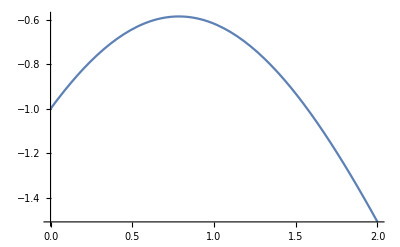

```mathematica
Plot[f[x],{x,0,2}]
```

```mathematica
eps = 0.00001;T=Table[{x,f[x]},{x,-0,1.5,0.75}];ep = 132;n=1;
```

```mathematica
ex = 423423;
```

```mathematica
While[ep > eps,
p = InterpolatingPolynomial[T,x];
res = Solve[p==0,x];
x1=x/.res[[2]];
ep = Abs[Abs[ex]-Abs[x1]];
T1 = Rest[T];
ex=x1;
T = Append[T1, {x1,N[f[x1]]}];
Print["xi = " ,x1, " eps_i = " ,ep, " i = ", n];
n=n+1]
```

xi = 0.783737+0.932254 ⅈ eps_i = 423422. i = 1

xi = 0.835196-0.909285 ⅈ eps_i = 0.0167215 i = 2

xi = 0.785645+0.875513 ⅈ eps_i = 0.0583127 i = 3

xi = 0.785401+0.881331 ⅈ eps_i = 0.00417459 i = 4

xi = 0.785398+0.881374 ⅈ eps_i = 0.0000296713 i = 5

xi = 0.785481-0.534806 ⅈ eps_i = 0.230275 i = 6

xi = 0.785406-0.865003 ⅈ eps_i = 0.21811 i = 7

xi = 0.785398+0.881374 ⅈ eps_i = 0.0121656 i = 8

xi = 0.785398+0.881374 ⅈ eps_i = 1.00057×10^-9 i = 9

```mathematica
ep
```

1.00057×10^-9

```mathematica
NSolve[f[x]==0,x]
```

{{x→ConditionalExpression[1. ((0.785398-0.881374 ⅈ)+6.28319 C[1]),C[1]∈ℤ]},{x→ConditionalExpression[1. ((0.785398+0.881374 ⅈ)+6.28319 C[1]),C[1]∈ℤ]}}